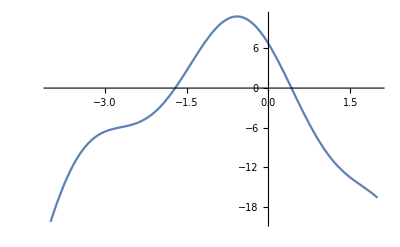

```mathematica
f[x_]:=5Cos[2x+1]-3 x^2-5x+4;
Plot[f[x], {x, -2, -1.6}]
```

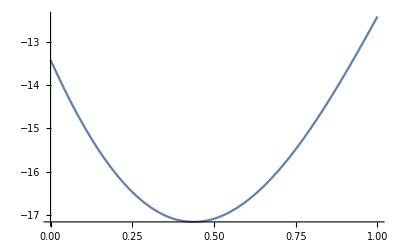

```mathematica
Plot[f'[x],{x,0,1}]
```

```mathematica
k=Abs[f'[0.45]]
```

Abs[f'[0.45]]

```mathematica
0.1<2/k
```

0.1<2/Abs[f'[0.45]]

9

-1.712

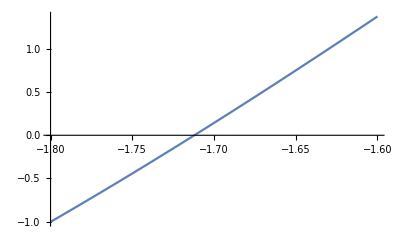

```mathematica
g[x_]=x-0.1(5Cos[2x+1]-3 x^2-5x+4);
x0=0.4;
x1=g[x0];
eps=0.001;
i=1;
While[Abs[x1-x0]>eps,
x0=x1;
x1=g[x0];
i++;
]

i 
Round[x1,eps]
Plot[f[x],{x,-1.8,-1.6}]
```